# Manifold at q=2 cycles

## Manifold solution

```mathematica
ClearAll[alpha,beta];
alpha[a1_]:=With[{a2=1-a1},1/12*a1^2-1/12*a1*a2-1/24*a2^2]
beta[a1_]:=With[{a2=1-a1},-1/24*a1+1/12*a2]
```

```mathematica
ClearAll[Manifold]
Manifold[a1val_]:=Sqrt[Abs[alpha[a1val]]^2+Abs[beta[a1val]]^2]
```

## Visualization

Visualizations of the complete manifold and each contribution.
The solver doesn’t know the difference between different points, which results in arbitrary indexing of the solutions.
Due to this reason, the branch colors change at certain points.

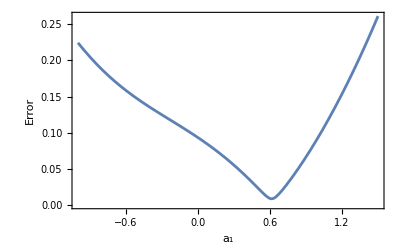

```mathematica
Plot[Manifold[a1],{a1,-1.0,1.5 } ,PlotStyle->PointSize[0.015],Frame->True,FrameLabel->{"a_1","Error"}]
```